### Plot

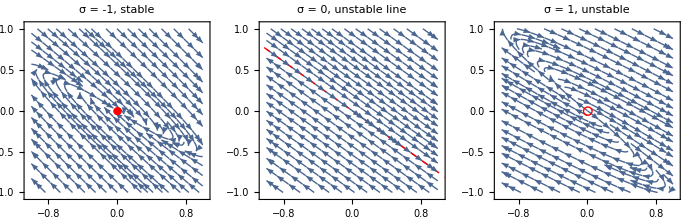

/Users/adam/Programming/CAS/Dynamical Systems/Assignment 1/degenerate_2_dim_plot.png

```mathematica
xDot[x_,y_,σ_]:=(σ+3)x + 4y
yDot[x_,y_,σ_]:=-(9/4)x + (σ-3)y
range = 1;
p1 = Show[StreamPlot[{xDot[x,y,-1], yDot[x,y,-1]}, {x,-range,range}, {y,-range,range},PlotLabel->"σ = -1, stable"],Graphics[{Red,Disk[{0,0},0.05]}]];
p2 = Show[StreamPlot[{xDot[x,y,0], yDot[x,y,0]}, {x,-range,range}, {y,-range,range}, PlotLabel->"σ = 0, unstable line", StreamPoints->10000],Graphics[{Red,Dashed,Line[{{-4,3},{4,-3}}]}]];
p3 = Show[StreamPlot[{xDot[x,y,1], yDot[x,y,1]}, {x,-range,range}, {y,-range,range},PlotLabel->"σ = 1, unstable"],Graphics[{Red,Circle[{0,0},0.05]}]];
g = GraphicsRow[{p1,p2,p3}]
Export["/Users/adam/Programming/CAS/Dynamical Systems/Assignment 1/degenerate_2_dim_plot.png",g,"PNG", ImageSize->{1500}]
```

### Matrix calculations 1

```mathematica
M={{(σ+3),4},{−(9/4),σ−3}}
​​
```

{{3+σ,4},{-9/4,-3+σ}}

​​

```mathematica
M  // MatrixForm
```

(3+σ | 4
-9/4 | -3+σ)

```mathematica
Eigenvalues[M]
```

{σ,σ}

```mathematica
Det[M-λ*IdentityMatrix[2]]==0
```

λ^2-2 λ σ+σ^2==0

```mathematica
IdentityMatrix[2]
```

{{1,0},{0,1}}

```mathematica
Eigenvectors[M]
```

{{-4/3,1},{0,0}}

```mathematica
Normalize[{-4/3,1}]
```

{-4/5,3/5}

```mathematica
Inverse[M]
```

{{(-3+σ)/σ^2,-4/σ^2},{9/(4 σ^2),(3+σ)/σ^2}}

### Matrix calculations 2

```mathematica
xDot[x_,y_,σ_,c_,d_]:=(σ−c d)x+d^2y;
yDot[x_,y_,σ_,c_,d_]:=−c^2x+(σ+c d)y;
M=.; c=.; d=.; σ=.;
M={{σ−c d, d^2},{−c^2,σ+c d}}
```

{{-c d+σ,d^2},{-c^2,c d+σ}}

```mathematica
Eigenvalues[M]
```

{σ,σ}

```mathematica
eig = Eigenvectors[M]
```

{{d/c,1},{0,0}}

```mathematica
{{d/c,1},{0,0}}
```

{{d/c,1},{0,0}}

```mathematica
Normalize[eig[[1]]]
```

{d/(c √(1+Abs[d/c]^2)),1/(√(1+Abs[d/c]^2))}

### New plot

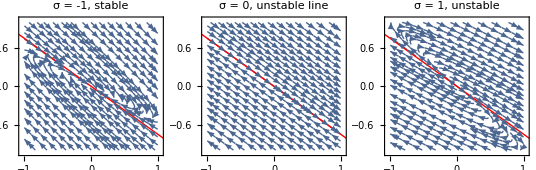

```mathematica
xDot[x_,y_,σ_]:=(σ+3)x + 4y
yDot[x_,y_,σ_]:=-(9/4)x + (σ-3)y
range = 1;
p1 = Show[StreamPlot[{xDot[x,y,-1], yDot[x,y,-1]}, {x,-range,range}, {y,-range,range},PlotLabel->"σ = -1, stable"],Graphics[{Red,Line[{{-4,3},{4,-3}}]}]];
p2 = Show[StreamPlot[{xDot[x,y,0], yDot[x,y,0]}, {x,-range,range}, {y,-range,range}, PlotLabel->"σ = 0, unstable line", StreamPoints->10000],Graphics[{Red,Line[{{-4,3},{4,-3}}]}]];
p3 = Show[StreamPlot[{xDot[x,y,1], yDot[x,y,1]}, {x,-range,range}, {y,-range,range},PlotLabel->"σ = 1, unstable"],Graphics[{Red,Line[{{-4,3},{4,-3}}]}]];
g = GraphicsRow[{p1,p2,p3}]
```